## 词语接龙

```mathematica
model=NetModel[{"GPT2 Transformer Trained on WebText Data","Task"->"LanguageModeling"}]
```

NetChain[…]

```mathematica
model["The best thing about AI is its ability to",{"TopProbabilities",5}];
Dataset[ReverseSort[Association[%]],ItemDisplayFunction->(PercentForm[#,2]&)]
```

```mathematica
NestList[StringJoin[#,model[#,"Decision"]]&,"The best thing about AI is its ability to",7]
```

{The best thing about AI is its ability to,The best thing about AI is its ability to learn,The best thing about AI is its ability to learn from,The best thing about AI is its ability to learn from experience,The best thing about AI is its ability to learn from experience.,The best thing about AI is its ability to learn from experience. It,The best thing about AI is its ability to learn from experience. It's,The best thing about AI is its ability to learn from experience. It's not}

```mathematica
ListLogLogPlot[Take[ReverseSort[model["The best thing about AI is its ability to","Probabilities"]],100],Frame->True]
```

-Graphics-

## 语言概率

## 字母

```mathematica
EntityValue[Entity["Language","English"],EntityProperty["Language","LetterFrequency"]]
```

{e→12.7 %,t→9.06 %,a→8.17 %,o→7.51 %,i→6.97 %,n→6.75 %,s→6.33 %,h→6.09 %,r→5.99 %,d→4.25 %,l→4.03 %,c→2.78 %,u→2.76 %,m→2.41 %,w→2.36 %,f→2.23 %,g→2.02 %,y→1.97 %,p→1.93 %,b→1.49 %,v→0.978 %,k→0.772 %,j→0.153 %,x→0.15 %,q→0.095 %,z→0.074 %}

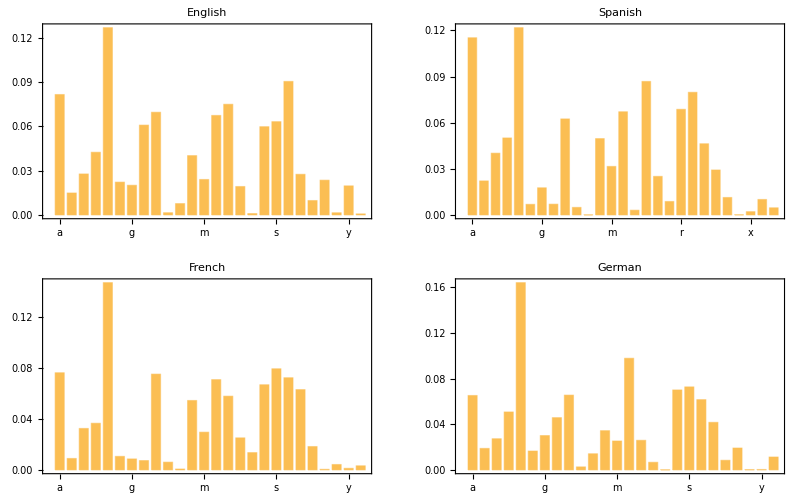

```mathematica
Map[Function[lang,BarChart[Normal[Values[KeySort[DeleteCases[EntityValue[Entity["Language",lang],EntityProperty["Language","LetterFrequency"]],_?(Not@StringContainsQ[Keys[#],Alphabet[lang]]&)](*排除字母表以外的字母*),AlphabeticOrder[lang]]]],ChartLabels->Alphabet[lang],Frame->True,PlotLabel->lang]],{"English","Spanish","French","German"}]//ArrayReshape[#,{2,2}]&//GraphicsGrid
```

## 字母对

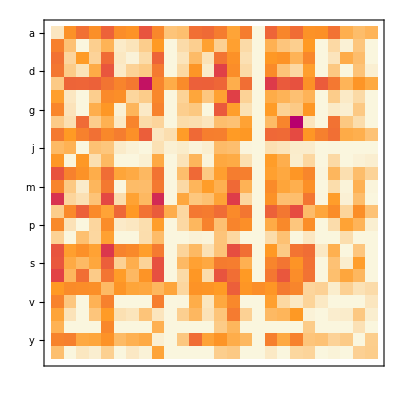

```mathematica
MatrixPlot[Transpose@With[{data=},
Outer[Lookup[Lookup[data,Key@{#1}],Key@{#2},0]&,Alphabet[],Alphabet[]]],FrameTicks->{{#,None},{None,#}}&[Table[{i,FromLetterNumber[i]},{i,26}]],
ColorFunction->{{"[◼]", "ChatTechColors"}}["Orange"]]
```

And we see here, for example, that the “q” column is blank (zero probability) except on the “u” row.